```mathematica
Integrate[Exp[Abs[x]] 1/(√(2π t))Exp[-x^2/(2t)],{x,-∞,∞},Assumptions->t>0]
```

-ⅇ^(t/2) (-2+GammaRegularized[1/2,t/2])

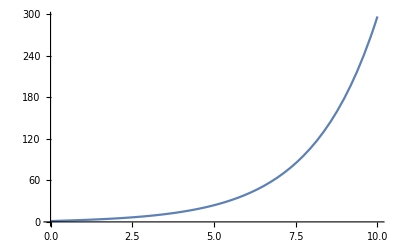

```mathematica
Plot[-ⅇ^(t/2) (-2+GammaRegularized[1/2,t/2]),{t,0,10}]
```

```mathematica
Integrate[Exp[-Abs[y]] 1/(√(2π t))Exp[(-(x-y)^2)/(2t)],{y,-∞,∞},Assumptions->t>0]
```

1/2 ⅇ^(t/2-x) (Erfc[(t-x)/(√2 √t)]+ⅇ^(2 x) Erfc[(t+x)/(√2 √t)])

```mathematica
1/2 ⅇ^(t/2-x) (Erfc[(t-x)/(√2 √t)]+ⅇ^(2 x) Erfc[(t+x)/(√2 √t)]) Exp[Abs[x]]//FullSimplify
```

```mathematica
Limit[1/2 ⅇ^(t/2-x) (Erfc[(t-x)/(√2 √t)]+ⅇ^(2 x) Erfc[(t+x)/(√2 √t)]) Exp[Abs[x]]/.t->1,x->∞]
```

√ⅇ

```mathematica
Limit[1/2 ⅇ^(t/2-x) (Erfc[(t-x)/(√2 √t)]+ⅇ^(2 x) Erfc[(t+x)/(√2 √t)]) Exp[Abs[x]],x->∞,Assumptions->t>0]
```

```mathematica
Plot3D[1/2 ⅇ^(t/2-x+Abs[x]) (Erfc[(t-x)/(√2 √t)]+ⅇ^(2 x) Erfc[(t+x)/(√2 √t)]),{t,0,3},{x,-100,100},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot3D[1/2 ⅇ^(t/2-x) (Erfc[(t-x)/(√2 √t)]+ⅇ^(2 x) Erfc[(t+x)/(√2 √t)]),{t,0,30},{x,-10,10},PlotRange->Full]
```

-Graphics3D-

```mathematica
Plot[ⅇ^(t/2) Erfc[(√t)/(√2)],{t,0,10}]
```

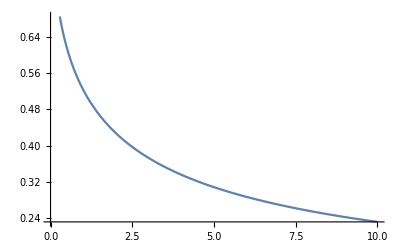

```mathematica
Plot[ⅇ^(t/2) Erfc[(√t)/(√2)],{t,0,10}]
```

```mathematica
Integrate[Exp[x] 1/(√(2π t))Exp[-x^2/(2t)],{x,-∞,∞},Assumptions->t>0]
```

ⅇ^(t/2)

```mathematica
Integrate[Exp[-x] 1/(√(2π t))Exp[-x^2/(2t)],{x,-∞,∞},Assumptions->t>0]
```

ⅇ^(t/2)

```mathematica
Integrate[1/(1+y^2)1/(√(2π t))Exp[(-(x-y)^2)/(2t)],{y,-∞,∞},Assumptions->t>0]
```

Integrate[(ⅇ^(-(x-y)^2/(2 t)))/(√(2 π) √t (1+y^2)),{y,-∞,∞},Assumptions→t>0]

```mathematica
Plot3D[(1+x^2)NIntegrate[1/(1+y^2)1/(√(2π t))Exp[(-(x-y)^2)/(2t)],{y,-∞,∞}],{t,0,1000},{x,-1000,1000},PlotRange->Full]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-Graphics3D-

```mathematica
Plot3D[NIntegrate[1/(1+y^2)1/(√(2π t))Exp[(-(x-y)^2)/(2t)],{y,-∞,∞}],{t,0,10},{x,-10,10}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-Graphics3D-

```mathematica
Plot3D[(1+x^2)NIntegrate[1/(1+y^2)1/(√(2π t))Exp[(-(x-y)^2)/(2t)],{y,-∞,∞}],{t,0,10},{x,-30,30},PlotRange->Full]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

-Graphics3D-

```mathematica
D[(1+x^2)Integrate[1/(1+y^2)1/(√(2π t))Exp[(-(x-y)^2)/(2t)],{y,-∞,∞}],x]
```

$Aborted

```mathematica
Limit[(1+x^2)Integrate[1/(1+y^2)1/(√(2π t))Exp[(-(x-y)^2)/(2t)],{y,-∞,∞}],x->∞]
```

$Aborted

```mathematica
Plot3D[(-(x-y)^2)/2+Abs[x],{y,-10,10},{x,-20,20}]
```

-Graphics3D-

```mathematica
D[(-(x-y)^2)/2+Abs[x],x]
```

-x+y+Abs'[x]

```mathematica
Solve[D[(-(x-y)^2)/2+Abs[x],x]==0,x]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[-x+y+Abs'[x]==0,x]

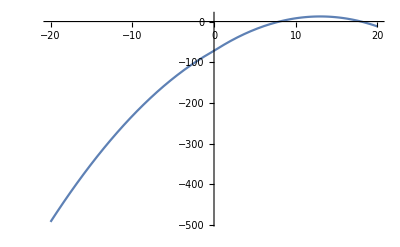

```mathematica
Plot[(-(x-y)^2)/2+Abs[x]/.y->12,{x,-20,20}]
```

```mathematica
Now check the admissalbe weight
```

```mathematica
Integrate[Exp[-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2)],{y,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2))ⅆy

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2)],{y,-∞,∞}],{x,0,100},PlotRange->Full]
```

-Graphics-

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

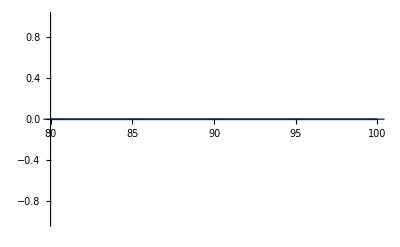

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2)],{y,-∞,∞}],{x,80,100},PlotRange->Full]
```

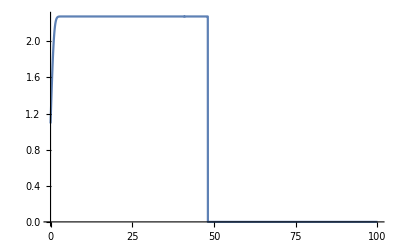

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2+Abs[x]-Abs[y]],{y,-∞,∞}],{x,0,100},PlotRange->Full]
```

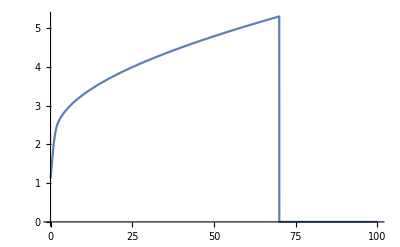

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2+Abs[x]^(8/7)-Abs[y]^(8/7)],{y,-∞,∞}],{x,0,100},PlotRange->Full]
```

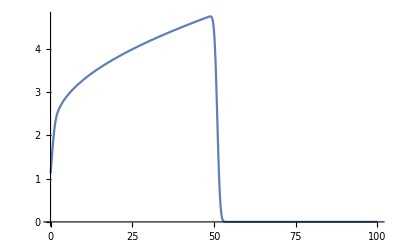

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2+Abs[x]^(8/7)-Abs[y]^(8/7)],{y,-50,50}],{x,0,100},PlotRange->Full]
```

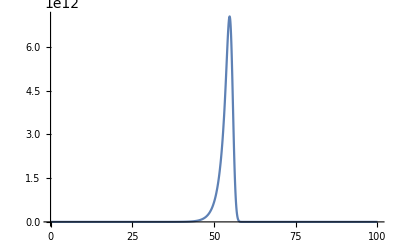

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2)],{y,-50,50}],{x,0,100},PlotRange->Full]
```

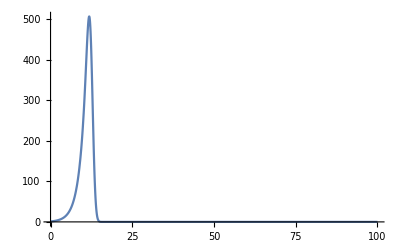

```mathematica
Plot[NIntegrate[Exp[-(x-y)^2+Abs[x]^(3/2)-Abs[y]^(3/2)],{y,-10,10}],{x,0,100},PlotRange->Full]
```

```mathematica
Limit[Abs[x]^(3/2)-Abs[x-y]^(3/2),x->∞,Assumptions->{y>0}]
```

∞

```mathematica
Limit[Abs[x]-Abs[x-y],x->∞,Assumptions->{y>0}]
```

y

```mathematica
Limit[Abs[x]^(1/2)-Abs[x-y]^(1/2),x->∞,Assumptions->{y>0}]
```

0

```mathematica
b=8/7
Limit[Abs[x]^b-Abs[x-y]^b,x->∞,Assumptions->{y>0}]
```

8/7

∞